```mathematica
SetDirectory[NotebookDirectory[]];
```

## Data from present code

### Mapping order 2

#### 1st order

```mathematica
convergenceglobalp1=Import["../outputs/convergence_tables/convergence_table_global_degree_1","Table"][[2;;-1,{1,3,5,6}]];

(*convergenceadaptivep1=Import["../outputs/convergence_tables/convergence_table_adaptive_degree_1","Table"][[2;;-1,{1,3,5,6}]];

convergenceadaptivekellyp1=Import["../outputs_convergence_study/convergence_tables/convergence_table_adaptive_kelly_degree_1","Table"][[2;;-1,{1,3,5,6}]];*)
```

#### 2nd order

```mathematica
convergenceglobalp2=Import["../outputs/convergence_tables/convergence_table_global_degree_2","Table"][[2;;-1,{1,3,5,6}]];

(*convergenceadaptivep2=Import["../outputs_convergence_study/convergence_tables/convergence_table_adaptive_degree_2","Table"][[2;;-1,{1,3,5,6}]];

convergenceadaptivekellyp2=Import["../outputs_convergence_study/convergence_tables/convergence_table_adaptive_kelly_degree_2","Table"][[2;;-1,{1,3,5,6}]];
*)
```

## Convergence Plots

### convergence plots from deal

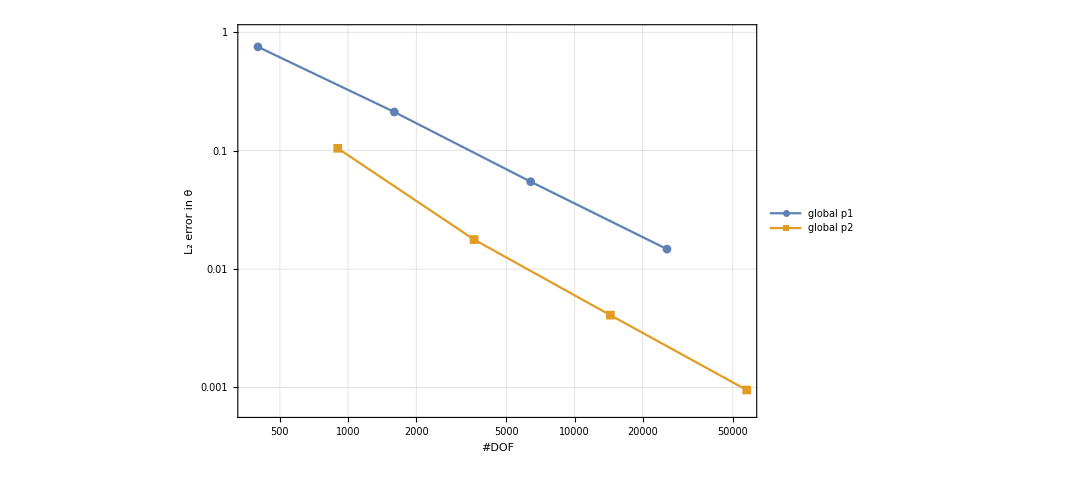

```mathematica
ListLogLogPlot[{convergenceglobalp1[[All,{3,1}]],convergenceglobalp2[[All,{3,1}]]},Joined->True,GridLines->Automatic,Frame->True,PlotLegends->{"global p1","global p2","adaptive p1","adaptive p2","adaptive kelly p1","adaptive kelly p2"},PlotMarkers->Automatic,ImageSize->800,FrameLabel->{"#DOF","L_2 error in θ"}]
```